# Tabbed UpSet Chart

```mathematica
Quit[];
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

## Load Data

```mathematica
dd=UpSetChart`TestData`DummyData[3]
```

<|Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Tasty→{Kiwi,Pear},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Vegetable→{Cucumber,Pickle}|>

## Do calculations

```mathematica
calc=UpSetChart`Calculations`CalcThenSortAndFilter[dd]
```

<|sets→<|Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Green→{Kiwi,Pear,Cucumber,Pickle},Red→{Strawberry,Apple},Tasty→{Kiwi,Pear},Vegetable→{Cucumber,Pickle}|>,comparisons→<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

```mathematica
gb=GroupBy[calc["comparisons"],Length[#]&]
```

<|3→<|{Fruit}→{Banana,Carrot,Lemon}|>,2→<|{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

```mathematica
GroupBy[calc["comparisons"],Length[#]&]
```

<|3→<|{Fruit}→{Banana,Carrot,Lemon}|>,2→<|{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

```mathematica
Key@calc["comparisons"]
```

Key[<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>]

```mathematica
gb=Map[Association@@Map[#-> calc["comparisons"][#]&,#]&,
GroupBy[Keys@calc["comparisons"],Length@#&]]
```

<|1→<|{Fruit}→{Banana,Carrot,Lemon}|>,2→<|{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry}|>,3→<|{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

## Calculate components by size

```mathematica
gc=UpSetChart`Graphics`Utilities`GraphicComponents;
```

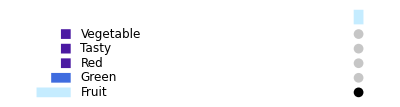
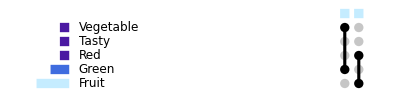
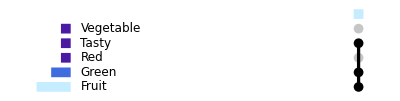
<|1→-Graphics-,2→-Graphics-,3→-Graphics-|>

```mathematica
(*gbgc=Graphics[#,ImageSize->{400,100}
(*, BaselinePosition->Bottom*)
(*, AlignmentPoint->{0,0}*)
]&/@(gc[calc["sets"],# ]&/@gb)*)
gbgc=Graphics[#
(*, BaselinePosition->Bottom*)
(*, AlignmentPoint->{0,0}*)
]&/@(gc[calc["sets"],#]&/@gb)
```

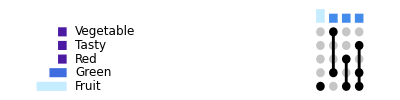

```mathematica
GraphicsColumn[Values[gbgc]]
```

```mathematica
TabView[KeySortBy[gbgc,#&],
Alignment->{Left,Bottom},
ContentPadding->False,
AutoAction->True,
BaselinePosition->Bottom,
ControlPlacement->Left,
ImageMargins->0,
FrameMargins-> 0
]
```

123